```mathematica
(*First we'll clear the Kernel of any unwanted definitions*)
(*Quit[]*)
```

Here, I consider the result of mutant invasion in a cycling population. This occurs when average specialist payoff exceeds average generalist payoff. First I’ll consider the outcome of  an invading alpha mutant along a cycle’s period. Below is our system of equations denoting the frequency of each strategist.

First we’ll create expressions for the frequency of the two specialist host phenotypes, and potential mutants in each phenotype. Each Strategist will have their own associated payoffs:

```mathematica
(*x -> the proportion of a host's resource that is shared*)
(*α -> the matched exchange rate*)
(*(1-α^(1/c))^c -> the mismatched exchange rate, f(α)*)
(*αg -> the generalist exchange rate*)
payoffs={x*(α−x),
x*((1-α^(1/c))^c−x),
x*(αg−x),
x*(1−α),
x*(1−(1-α^(1/c))^c),
x*(1−αg)};(*Payoffs for hosts (1 through 3)and symbionts (4 through 6)*)
```

```mathematica
{pi1,pi1',pig,ψ1,ψ1',ψg1}=payoffs; (*Host 1 payoffs: pi1 = match, pi1' = msimatch and pig = generalist. Payoffs for a symbiont interacting with host 1: ψ1 = match,ψ1' = mismatch,ψg1 = generalist)*)
{pi1m,pi1m',pig1m,ψ1m,ψ1m',ψg1m}=payoffs/.{α-> αm};
{pi2,pi2',pig2,ψ2,ψ2',ψg2}=payoffs/.{α->α2 };
{pi2m,pi2m',pig2m,ψ2m,ψ2m',ψg2m}=payoffs/.{α->α2m };
(*Payoffs for interactions with and by host 1 (denoted by 1), the host 1 mutant (denoted by 1m), host 2 (denoted by 2)and the host 2 mutant (denoted by 2m)*)
```

Next we find the average payoffs of each strategist:

```mathematica
S1 = v1*ψ1+v2*ψ2'+m1*ψ1m+m2*ψ1m'+(1−v−p-m1-m2)*ψg1; (*Symbiont 1 *)
S2 =  v1*ψ1'+v2*ψ2+m1*ψ1m'+m2*ψ2m+(1−v−p-m1-m2)*ψg1; (*Symbiont 2 *)
H1=u*pi1+(1-u)*pi1';(*Host 1 *)
H2 = u*pi2'+(1−u)*pi2;(*Host 2 *)
HM1=u*pi1m+(1-u)*pi1m';(*Host 1 mutant*)
HM2=u*pi2m+(1-u)*pi2m';(*Host 2 mutant*)
HG = pig;(*Generalist Host*)
Hbar = v1*H1+v2*H2+m1*HM1+m2*HM2+(1-v1-v2-m1-m2)*HG;(*Payoff received by a host on average*)
```

Finally, we’ll find expressions for the frequency of each strategist:

```mathematica
S = u(1-u)(S1-S2);(*Symbiont 1*)
V1=v1(H1-Hbar);(*Host 1*)
V2=v2(H2-Hbar);(*Host 2*)
M1=m1(HM1-Hbar);(*Host 1 Mutant*)
M2=m2(HM2-Hbar); (*Host 2 Mutant*)
```

Now we can put these equations together in a system:

```mathematica
replicators={S,V1,V2,M1,M2}/.{v1-> v1[t],v2-> v2[t],m1-> m1[t],m2-> m2[t], u-> u[t]};
```

```mathematica
{u'[t]==replicators[[1]],v1'[t]==replicators[[2]],v2'[t]==replicators[[3]],m1'[t]==replicators[[4]],m2'[t]==replicators[[5]],u[0]==u0,v1[0]==v10-m10,m1[0]==m10,m2[0]==m20};
```

```mathematica
System[α_,αm_, α2_,α2m_,αg_,c_,x_,u0_,v10_,v20_,m10_,m20_]:={u'[t]==(1-u[t]) u[t] (x (1-αm) m1[t]-x (1-(1-αm^(1/c))^c) m1[t]-x (1-α2m) m2[t]+x (1-(1-αm^(1/c))^c) m2[t]+x (1-α) v1[t]-x (1-(1-α^(1/c))^c) v1[t]-x (1-α2) v2[t]+x (1-(1-α2^(1/c))^c) v2[t]),v1'[t]==v1[t] (x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]-m2[t] (x (-x+(1-α2m^(1/c))^c) (1-u[t])+x (-x+α2m) u[t])-m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t])-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-m1[t]-m2[t]-v1[t]-v2[t])-(x (-x+α2) (1-u[t])+x (-x+(1-α2^(1/c))^c) u[t]) v2[t]),v2'[t]==v2[t] (x (-x+α2) (1-u[t])+x (-x+(1-α2^(1/c))^c) u[t]-m2[t] (x (-x+(1-α2m^(1/c))^c) (1-u[t])+x (-x+α2m) u[t])-m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t])-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-m1[t]-m2[t]-v1[t]-v2[t])-(x (-x+α2) (1-u[t])+x (-x+(1-α2^(1/c))^c) u[t]) v2[t]),m1'[t]==m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t]-m2[t] (x (-x+(1-α2m^(1/c))^c) (1-u[t])+x (-x+α2m) u[t])-m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t])-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-m1[t]-m2[t]-v1[t]-v2[t])-(x (-x+α2) (1-u[t])+x (-x+(1-α2^(1/c))^c) u[t]) v2[t]),m2'[t]==m2[t] (x (-x+(1-α2m^(1/c))^c) (1-u[t])+x (-x+α2m) u[t]-m2[t] (x (-x+(1-α2m^(1/c))^c) (1-u[t])+x (-x+α2m) u[t])-m1[t] (x (-x+(1-αm^(1/c))^c) (1-u[t])+x (-x+αm) u[t])-(x (-x+(1-α^(1/c))^c) (1-u[t])+x (-x+α) u[t]) v1[t]-x (-x+αg) (1-m1[t]-m2[t]-v1[t]-v2[t])-(x (-x+α2) (1-u[t])+x (-x+(1-α2^(1/c))^c) u[t]) v2[t]),WhenEvent[{m1[t]≤0,m1[t]≥1},m1'[t]->0],u[0]==u0,v1[0]==-m10+v10,v2[0]==v20,m1[0]==m10,m2[0]==m20}(*Here, we format this system appropriately for our simulations note that we begin from initial conditions for u, Subscript[v, 1], v2, v1m and v2m given by u0, v10, v20, v1m0 and v2m0 respectively*)
```

Now we will set up our system with reasonable initial parameters, the tradeoff between matched and mismatching will be concave up.  For now the mutant hosts will be absent. The only hosts present will be host 1 and hosts 2. First we’ll observe the normal cycling of this population:

```mathematica
(*First we test the system to make sure no inappropriate characters remain*)
(*System[α_,αm_, α2_,α2m_,α_,c_,x_,u0_,v10_,v20_,m10_,m20_]*)
System[0.6,0, 0.6,0,0.3,2,0.5,0.6,0.4,0.34,0,0];
```

```mathematica
(*Next we solve this system: *)
sol=NDSolve[System[0.6,0.9, 0.6,0.9,0.3,2,0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
```

```mathematica
(*Store the functions for u(t), Subscript[v, 1](t), Subscript[v, 2](t),Subscript[v, 1] m(t), Subscript[v, 2] m(t)*)
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
```

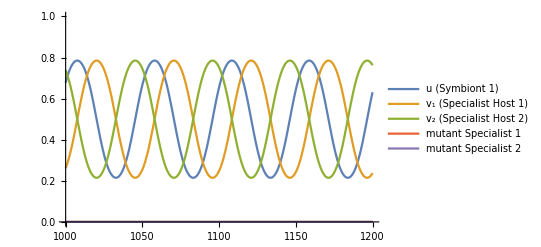

```mathematica
(*Plot*)
Plot[{uans,v1ans,v2ans,m1ans,m2ans},{t,1000,1200}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
(*Reviewing the plot below, note that these initial parameters predispose our system toward having an especially large amplitude, which will make invasion more difficult for mutants that extract more than residents since if they invade at a trough, the population will be largely composed of the symbiont they prefer less. *)
```

Next, we’ll add a mutant host at a point in the cycle:

{0.774366,0.406849,0.593151,0.,0.}

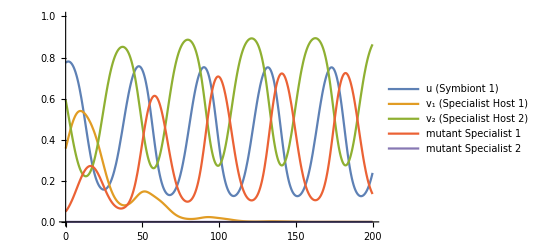

```mathematica
sol=NDSolve[System[0.6,0.9, 0.6,0.9,0.3,2,0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
{uf, v1f,v2f,m1f,m2f}={u[1257],v1[1257],v2[1257],m1[1257],m2[1257]}/.Flatten[sol] (*Find the value of the function when t=1257*)
(*Add a new host 1 mutant at this point in time whose frequency is 0.05: *)
sol=NDSolve[System[0.6,0.9, 0.6,0,0.3,2,0.5,uf,v1f,v2f,0.05,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
Plot[{uans,v1ans,v2ans,m1ans,m2ans},{t,0,200}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
```

We see here that this host introduced at an arbitrary time point successfully invades. Now let’s more systematically consider the outcome of invasion across a cycle’s period. To do so first we need to find the length of a cycle’s period, and define a function to find the average of an NDSolve output.

```mathematica
(*A function to find the average of an interpolating function over a given period in time from a to b:*)
FindAverage[fun_,a_,b_]:=(1/(b-a))*NIntegrate[fun,{t,a,b},WorkingPrecision->4];
(*Next we'll find the cycle's period by comparing the difference in time between two different extrema: *)
sol=NDSolve[System[0.6,0.9, 0.6,0.9,0.3,2,0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
Plot[{uans,v1ans,v2ans,m1ans,m2ans},{t,1000,1200}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
(*Period of v1(t): *)
FindMinimum[{v1ans,1030≤t≤1060},t](*First trough*)
FindMinimum[{v1ans,1070≤t≤1100},t](*Second Trough*)
(*Period of v2(t): *)
FindMinimum[{v2ans,1005≤t≤1050},t]
FindMinimum[{v2ans,1055≤t≤1100},t]
(*Period of u(t) *)
FindMinimum[{uans,1010≤t≤1050},t]
FindMinimum[{uans,1060≤t≤1100},t]
```

-Graphics-

{0.214796,{t→1045.35}}

{0.214796,{t→1095.73}}

{0.214796,{t→1020.17}}

{0.214796,{t→1070.54}}

{0.214797,{t→1032.76}}

{0.214797,{t→1083.13}}

A great sanity check! All of the functions have the same period of 50.4 timesteps. Now let’s consider what happens when we introduce a host 1 mutant with an increased value of alpha along the entirety of this period. First, we’ll see if the frequency of the mutant briefly increases, decreases after the mutant is introduced:

```mathematica
Do[sol=NDSolve[System[0.6,0.9, 0.6,0.9,0.3,2,0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
(*Note that in order to consider the most extreme scenario that would lead to mutant extinction, mutants have a value of alpha that is 0.5 times greater than that of residents. *)
{uf, v1f,v2f,m1f,m2f}={u[st],v1[st],v2[st],m1[st],m2[st]}/.Flatten[sol];
                   sol=NDSolve[System[0.6,0.9, 0.6,0,0.3,2,0.5,uf,v1f,v2f,0.05,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
{min,time}=FindMinimum[{m1ans,10≤t≤100},t];
If[min <0.05,Print["t0 = ", st, ", min = ", min],Unevaluated[Sequence[]]];
,
{st,1255,1306,1}];
```

t0 = 1264, min = 0.0383412

t0 = 1265, min = 0.03533

t0 = 1266, min = 0.0326149

t0 = 1267, min = 0.0302014

t0 = 1268, min = 0.0280862

t0 = 1269, min = 0.0262592

t0 = 1270, min = 0.0247064

t0 = 1271, min = 0.0234122

t0 = 1272, min = 0.0223606

t0 = 1273, min = 0.021537

t0 = 1274, min = 0.0209285

t0 = 1275, min = 0.020525

t0 = 1276, min = 0.0203197

t0 = 1277, min = 0.0203098

t0 = 1278, min = 0.0204967

NDSolve::ndsz: At t == 859.584, step size is effectively zero; singularity or stiff system suspected.

t0 = 1279, min = 0.0208863

t0 = 1280, min = 0.0214888

t0 = 1281, min = 0.0223187

t0 = 1282, min = 0.023394

NDSolve::ndsz: At t == 799.063, step size is effectively zero; singularity or stiff system suspected.

t0 = 1283, min = 0.0247338

NDSolve::ndsz: At t == 540.018, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve::ndsz will be suppressed during this calculation.

t0 = 1284, min = 0.0263568

t0 = 1285, min = 0.0282792

t0 = 1286, min = 0.0308823

t0 = 1287, min = 0.0345957

t0 = 1288, min = 0.039677

t0 = 1289, min = 0.046439

So we see that there are certain points along a cycle in which being more extractive than a resident host leads to a dip in mutant invader frequency, though these introduced hosts all eventually manage to supplant residents. If the frequency of invading mutants is sufficiently low, or if cycles have a particularly large amplitude the mutants will go extinct.  Let’s see if sometimes introducing a mutant results in a lower average mutant frequency along the entirety of a cycle.

```mathematica
Do[sol=NDSolve[System[0.6,0.9, 0.6,0.9,0.3,2,0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
{uf, v1f,v2f,m1f,m2f}={u[st],v1[st],v2[st],m1[st],m2[st]}/.Flatten[sol];
                   sol=NDSolve[System[0.6,0.9, 0.6,0,0.3,2,0.5,uf,v1f,v2f,0.05,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
avg=FindAverage[m1ans,400,600];(*Average mutant frequency for 4 cycle periods after the mutant has introduced itself*)

Print["t0 = ",st," average mutant frequency after invasion is ",avg]
,
{st,1255,1306,3}];
```

t0 = 1255 average mutant frequency after invasion is 0.3743

t0 = 1258 average mutant frequency after invasion is 0.3731

t0 = 1261 average mutant frequency after invasion is 0.3773

t0 = 1264 average mutant frequency after invasion is 0.3817

t0 = 1267 average mutant frequency after invasion is 0.3828

t0 = 1270 average mutant frequency after invasion is 0.3858

t0 = 1273 average mutant frequency after invasion is 0.3874

t0 = 1276 average mutant frequency after invasion is 0.3898

NDSolve::ndsz: At t == 859.584, step size is effectively zero; singularity or stiff system suspected.

t0 = 1279 average mutant frequency after invasion is 0.3848

t0 = 1282 average mutant frequency after invasion is 0.3791

t0 = 1285 average mutant frequency after invasion is 0.3757

NDSolve::ndsz: At t == 895.624, step size is effectively zero; singularity or stiff system suspected.

t0 = 1288 average mutant frequency after invasion is 0.3794

t0 = 1291 average mutant frequency after invasion is 0.3793

t0 = 1294 average mutant frequency after invasion is 0.3783

t0 = 1297 average mutant frequency after invasion is 0.3795

t0 = 1300 average mutant frequency after invasion is 0.3819

t0 = 1303 average mutant frequency after invasion is 0.3789

t0 = 1306 average mutant frequency after invasion is 0.3736

So on t whole, even in conditions that predispose mutants toward extinction, mutants that extract more are able to invade, though certain invasion times appear more advantageous than others. And mutants with greater extractive capability will usually invade, increasing a cycle’s period. Let’s consider what will happen in a system when hosts are already highly extractive:

```mathematica
Do[sol=NDSolve[System[0.9,0.95, 0.9,0.9,0.3,2,0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
(*Note that in order to consider the most extreme scenario that would lead to mutant extinction, mutants have a value of alpha that is 0.5 times greater than that of residents. *)
{uf, v1f,v2f,m1f,m2f}={u[st],v1[st],v2[st],m1[st],m2[st]}/.Flatten[sol];
                   sol=NDSolve[System[0.9,0.95, 0.9,0,0.3,2,0.5,uf,v1f,v2f,0.05,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
{min,time}=FindMinimum[{m1ans,10≤t≤100},t];
If[min <0.05,Print["t0 = ", st, ", min = ", min],Unevaluated[Sequence[]]];
,
{st,1255,1306,1}];
```

t0 = 1255, min = 0.0177921

t0 = 1256, min = 0.0167052

t0 = 1257, min = 0.0159457

t0 = 1258, min = 0.0154526

t0 = 1259, min = 0.0151887

t0 = 1260, min = 0.015138

t0 = 1261, min = 0.0153045

t0 = 1262, min = 0.0157117

t0 = 1263, min = 0.0164039

t0 = 1264, min = 0.0174471

t0 = 1265, min = 0.0192427

t0 = 1266, min = 0.0226353

t0 = 1267, min = 0.0282233

t0 = 1268, min = 0.0368288

t0 = 1269, min = 0.0494165

t0 = 1278, min = 0.0487121

t0 = 1280, min = 0.0361465

t0 = 1281, min = 0.0309539

t0 = 1282, min = 0.0267159

t0 = 1283, min = 0.0233856

t0 = 1284, min = 0.0208389

t0 = 1285, min = 0.0189306

t0 = 1286, min = 0.0175264

t0 = 1287, min = 0.0165164

t0 = 1288, min = 0.0158187

t0 = 1289, min = 0.0153773

t0 = 1290, min = 0.0151599

t0 = 1291, min = 0.015155

t0 = 1292, min = 0.0153706

t0 = 1293, min = 0.0158348

t0 = 1294, min = 0.0165962

t0 = 1295, min = 0.017728

t0 = 1296, min = 0.019821

t0 = 1297, min = 0.0236284

t0 = 1298, min = 0.0297895

t0 = 1299, min = 0.03917

Thus, even in conditions which could lead to extinction of a mutant mutants with more extraction will invade. Consider the alternative, in which a less extractive mutant invades:

```mathematica
Do[sol=NDSolve[System[0.9,0.85, 0.9,0.9,0.3,2,0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
(*Note that in order to consider the most extreme scenario that would lead to mutant extinction, mutants have a value of alpha that is 0.5 times greater than that of residents. *)
{uf, v1f,v2f,m1f,m2f}={u[st],v1[st],v2[st],m1[st],m2[st]}/.Flatten[sol];
                   sol=NDSolve[System[0.9,0.85, 0.9,0,0.3,2,0.5,uf,v1f,v2f,0.05,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
avg=FindAverage[m1ans,400,600];(*Average mutant frequency for 4 cycle periods after the mutant has introduced itself*)

Print["t0 = ",st," average mutant frequency after invasion is ",avg]
,
{st,1255,1306,1}];
```

t0 = 1255 average mutant frequency after invasion is 0.0001522

t0 = 1256 average mutant frequency after invasion is 0.0001395

t0 = 1257 average mutant frequency after invasion is 0.0001344

t0 = 1258 average mutant frequency after invasion is 0.0001312

t0 = 1259 average mutant frequency after invasion is 0.0001295

t0 = 1260 average mutant frequency after invasion is 0.0001293

t0 = 1261 average mutant frequency after invasion is 0.0001315

t0 = 1262 average mutant frequency after invasion is 0.0001347

t0 = 1263 average mutant frequency after invasion is 0.0001397

t0 = 1264 average mutant frequency after invasion is 0.0001483

t0 = 1265 average mutant frequency after invasion is 0.0001609

t0 = 1266 average mutant frequency after invasion is 0.0001787

t0 = 1267 average mutant frequency after invasion is 0.0002029

t0 = 1268 average mutant frequency after invasion is 0.000235

t0 = 1269 average mutant frequency after invasion is 0.0002759

t0 = 1270 average mutant frequency after invasion is 0.0003251

t0 = 1271 average mutant frequency after invasion is 0.0003805

t0 = 1272 average mutant frequency after invasion is 0.0004363

t0 = 1273 average mutant frequency after invasion is 0.0004723

t0 = 1274 average mutant frequency after invasion is 0.0005106

t0 = 1275 average mutant frequency after invasion is 0.000511

t0 = 1276 average mutant frequency after invasion is 0.0004857

t0 = 1277 average mutant frequency after invasion is 0.0004414

t0 = 1278 average mutant frequency after invasion is 0.0003872

t0 = 1279 average mutant frequency after invasion is 0.0003337

t0 = 1280 average mutant frequency after invasion is 0.0002851

t0 = 1281 average mutant frequency after invasion is 0.0002445

t0 = 1282 average mutant frequency after invasion is 0.0002122

t0 = 1283 average mutant frequency after invasion is 0.0001873

t0 = 1284 average mutant frequency after invasion is 0.0001687

t0 = 1285 average mutant frequency after invasion is 0.000155

t0 = 1286 average mutant frequency after invasion is 0.0001496

t0 = 1287 average mutant frequency after invasion is 0.0001392

t0 = 1288 average mutant frequency after invasion is 0.0001336

t0 = 1289 average mutant frequency after invasion is 0.0001307

t0 = 1290 average mutant frequency after invasion is 0.0001294

t0 = 1291 average mutant frequency after invasion is 0.0001295

t0 = 1292 average mutant frequency after invasion is 0.0001321

t0 = 1293 average mutant frequency after invasion is 0.0001357

t0 = 1294 average mutant frequency after invasion is 0.0001412

t0 = 1295 average mutant frequency after invasion is 0.0001507

t0 = 1296 average mutant frequency after invasion is 0.0001643

t0 = 1297 average mutant frequency after invasion is 0.0001834

t0 = 1298 average mutant frequency after invasion is 0.0002092

t0 = 1299 average mutant frequency after invasion is 0.0002431

t0 = 1300 average mutant frequency after invasion is 0.0002856

t0 = 1301 average mutant frequency after invasion is 0.0003365

t0 = 1302 average mutant frequency after invasion is 0.0003929

t0 = 1303 average mutant frequency after invasion is 0.0004474

t0 = 1304 average mutant frequency after invasion is 0.0004906

t0 = 1305 average mutant frequency after invasion is 0.0005126

t0 = 1306 average mutant frequency after invasion is 0.0005075

The less extractive mutants always fail to invade. Next, consider the outcome of mutant invasion when the tradeoff between matching and mismatching is concave down (i.e. c = 1/2). Let we consider the outcome of a single mutant’s invasion:

{0.397967,0.242056,0.757944,0.,0.}

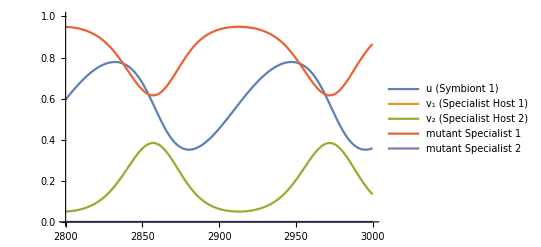

```mathematica
(*For future simulations I'm using a different value for resident α, α=0.4. This is so that we can experiment with a variety of different values of α both above and below this value*)
sol=NDSolve[System[0.5,0.7, 0.5,0.9,0.3,(1/2),0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
{uf, v1f,v2f,m1f,m2f}={u[1257],v1[1257],v2[1257],m1[1257],m2[1257]}/.Flatten[sol] (*Find the value of the function when t=1257*)
(*Add a new host 1 mutant at this point in time whose frequency is 0.05: *)
sol=NDSolve[System[0.4,0.65, 0.4,0,0.3,(1/2),0.5,uf,v1f,v2f,0.05,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
Plot[{uans,v1ans,v2ans,m1ans,m2ans},{t,2800,3000}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
```

Superficially it appears as though more extractive mutants always invade. However, let’s put this expectation to the test more rigorously. First we’ll determine the length of a cycle’s period so we can test the outcome of mutant invasion along an entire cycle.

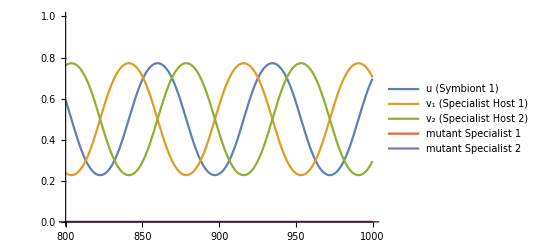

{0.227649,{t→878.599}}

{0.227649,{t→953.434}}

```mathematica
(*Next we'll find the cycle's period by comparing the difference in time between two different extrema: *)
sol=NDSolve[System[0.5,0.9, 0.5,0.9,0.3,(1/2),0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
Plot[{uans,v1ans,v2ans,m1ans,m2ans},{t,800,1000}, PlotRange -> {0,1}, Background->None,PlotLegends->LineLegend[{"u (Symbiont 1)","v_1 (Specialist Host 1)","v_2 (Specialist Host 2)","mutant Specialist 1","mutant Specialist 2"}]]
(*Period of v1(t): *)
FindMinimum[{v1ans,850≤t≤900},t](*First trough*)
FindMinimum[{v1ans,930≤t≤970},t](*Second Trough*)
```

Our period is therefore: 74.8348 timesteps. Next, we’ll vary the value of an invading host 1’s α to see which values allow this invading host to invade and supplant a resident host.

```mathematica
Do[sol=NDSolve[System[0.5,0.65, 0.5,0,0.3,(1/2),0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,1000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
{uf, v1f,v2f,m1f,m2f}={u[800],v1[800],v2[800],m1[800],m2[800]}/.Flatten[sol] ;(*Find the value of the function when t=1257*)
(*Add a new host 1 mutant at this point in time whose frequency is 0.05: *)
sol=NDSolve[System[0.5,nm, 0.5,0,0.3,(1/2),0.5,uf,v1f,v2f,0.05,0],{u,v1,v2,m1,m2},{t,0,1000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];

avg=FindAverage[m1ans,760,1000];
If[avg>0.05,Print[nm," results in invasion with frequency: ",avg] , Unevaluated[Sequence[]]];
(*Print[avg];*)
, {nm,0.3,0.9,0.01}]

(*Average mutant frequency for 2 cycle periods after the mutant has introduced itself*)
(*If[avg>0.05,Print[m," results in invasion with frequency: ",avg], Unevaluated[Sequence[]]];*)
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

0.5 results in invasion with frequency: 0.1037

0.51 results in invasion with frequency: 0.1925

0.52 results in invasion with frequency: 0.304

0.53 results in invasion with frequency: 0.4123

0.54 results in invasion with frequency: 0.4814

0.55 results in invasion with frequency: 0.5213

0.56 results in invasion with frequency: 0.5776

0.57 results in invasion with frequency: 0.5992

0.58 results in invasion with frequency: 0.5775

0.59 results in invasion with frequency: 0.623

0.6 results in invasion with frequency: 0.6748

0.61 results in invasion with frequency: 0.6515

0.62 results in invasion with frequency: 0.6847

0.63 results in invasion with frequency: 0.7175

0.64 results in invasion with frequency: 0.7487

0.65 results in invasion with frequency: 0.7617

0.66 results in invasion with frequency: 0.7853

0.67 results in invasion with frequency: 0.8593

0.68 results in invasion with frequency: 0.8547

0.69 results in invasion with frequency: 0.9133

0.7 results in invasion with frequency: 0.9491

0.71 results in invasion with frequency: 0.9986

0.72 results in invasion with frequency: 0.9273

0.73 results in invasion with frequency: 0.8952

0.74 results in invasion with frequency: 0.8213

0.75 results in invasion with frequency: 0.8322

0.76 results in invasion with frequency: 0.7512

0.77 results in invasion with frequency: 0.7372

0.78 results in invasion with frequency: 0.7042

0.79 results in invasion with frequency: 0.6868

0.8 results in invasion with frequency: 0.6123

0.81 results in invasion with frequency: 0.6473

0.82 results in invasion with frequency: 0.5676

0.83 results in invasion with frequency: 0.5057

0.84 results in invasion with frequency: 0.4137

0.85 results in invasion with frequency: 0.2197

0.86 results in invasion with frequency: 0.07316

```mathematica
ans=D[(1-α^(1/0.5))^(0.5),α];
ans/.α-> 0.71
```

-1.00823

So we observe that the mutant achieves the greatest frequency after invasion with an intermediate value of α around 0.71. At this value of α the value of f’(α) is closest to -1, as expected from the analytic adaptive dynamics work included in SI.2.

Is this value of α optimal at any point of invasion? Let’s find out. We’ll maek the resident value of α 0.71, and vary both the time of invasion and the value of α of invading mutants.

```mathematica
Do[sol=NDSolve[System[0.71,0.65, 0.71,0,0.3,(1/2),0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,1000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
{uf, v1f,v2f,m1f,m2f}={u[st],v1[st],v2[st],m1[st],m2[st]}/.Flatten[sol] ;
(*Add a new host 1 mutant at this point in time whose frequency is 0.05: *)
sol=NDSolve[System[0.71,nm, 0.71,0,0.3,(1/2),0.5,uf,v1f,v2f,0.05,0],{u,v1,v2,m1,m2},{t,0,1000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
avg=FindAverage[m1ans,760,1000];
If[avg>0.05,Print[nm," results in invasion with frequency: ",avg] , Unevaluated[Sequence[]]];
(*Print[avg];*)
, {nm,0.3,0.9,0.01},{st,800,875,1}]
```

0.71 results in invasion with frequency: 0.0500285

0.71 results in invasion with frequency: 0.0500897

0.71 results in invasion with frequency: 0.050151

0.71 results in invasion with frequency: 0.0502124

0.71 results in invasion with frequency: 0.0502738

0.71 results in invasion with frequency: 0.0503353

0.71 results in invasion with frequency: 0.0503969

0.71 results in invasion with frequency: 0.0504585

0.71 results in invasion with frequency: 0.0505203

0.71 results in invasion with frequency: 0.0505821

0.71 results in invasion with frequency: 0.0506439

0.71 results in invasion with frequency: 0.0507059

0.71 results in invasion with frequency: 0.0507679

0.71 results in invasion with frequency: 0.05083

0.71 results in invasion with frequency: 0.0508921

0.71 results in invasion with frequency: 0.0509544

0.71 results in invasion with frequency: 0.0510167

0.71 results in invasion with frequency: 0.0510791

0.71 results in invasion with frequency: 0.0511415

0.71 results in invasion with frequency: 0.0512041

0.71 results in invasion with frequency: 0.0512667

0.71 results in invasion with frequency: 0.0513293

0.71 results in invasion with frequency: 0.0513921

0.71 results in invasion with frequency: 0.0514549

0.71 results in invasion with frequency: 0.0515178

0.71 results in invasion with frequency: 0.0515807

0.71 results in invasion with frequency: 0.0516437

0.71 results in invasion with frequency: 0.0517068

0.71 results in invasion with frequency: 0.05177

0.71 results in invasion with frequency: 0.0518333

0.71 results in invasion with frequency: 0.0518966

0.71 results in invasion with frequency: 0.05196

0.71 results in invasion with frequency: 0.0520234

0.71 results in invasion with frequency: 0.0520869

0.71 results in invasion with frequency: 0.0521505

0.71 results in invasion with frequency: 0.0522142

0.71 results in invasion with frequency: 0.0522779

0.71 results in invasion with frequency: 0.0523417

0.71 results in invasion with frequency: 0.0524056

0.71 results in invasion with frequency: 0.0524695

0.71 results in invasion with frequency: 0.0525335

0.71 results in invasion with frequency: 0.0525976

0.71 results in invasion with frequency: 0.0526617

0.71 results in invasion with frequency: 0.0527259

0.71 results in invasion with frequency: 0.0527902

0.71 results in invasion with frequency: 0.0528546

0.71 results in invasion with frequency: 0.052919

0.71 results in invasion with frequency: 0.0529835

Mutants were only able to invade neutrally when they had the same value of α as residents. Thir frequency remained near that of the intial hosts they supplanted.

Finally, we consider invasion in the case in which the tradeoff between matching and mismatching is linear (c=1). This should result in neutral invasion of any potential mutant value of α. Mutants with any value of alpha can successfully invade.

```mathematica
Do[sol=NDSolve[System[0.6,0, 0.6,0,0.3,1,0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,1000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
{uf, v1f,v2f,m1f,m2f}={u[800],v1[800],v2[800],m1[800],m2[800]}/.Flatten[sol] ;
(*Add a new host 1 mutant at this point in time whose frequency is 0.05: *)
sol=NDSolve[System[0.6,nm, 0.6,0,0.3,1,0.5,uf,v1f,v2f,0.05,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
avg=FindAverage[m1ans,2800,3000];
If[avg>0.04,Print["α = ",nm," results in invasion with frequency: ",avg] , Unevaluated[Sequence[]]];
(*Print[avg];*)
, {nm,0,0.9,0.01}]
```

α = 0.01 results in invasion with frequency: 0.04783

α = 0.04 results in invasion with frequency: 0.07707

α = 0.05 results in invasion with frequency: 0.0683

α = 0.06 results in invasion with frequency: 0.08791

α = 0.07 results in invasion with frequency: 0.07477

α = 0.1 results in invasion with frequency: 0.07256

α = 0.11 results in invasion with frequency: 0.08027

α = 0.12 results in invasion with frequency: 0.08511

α = 0.13 results in invasion with frequency: 0.08085

α = 0.14 results in invasion with frequency: 0.09246

α = 0.15 results in invasion with frequency: 0.08393

α = 0.16 results in invasion with frequency: 0.08786

α = 0.17 results in invasion with frequency: 0.08939

α = 0.18 results in invasion with frequency: 0.08819

α = 0.19 results in invasion with frequency: 0.09132

α = 0.2 results in invasion with frequency: 0.09119

α = 0.21 results in invasion with frequency: 0.09133

α = 0.22 results in invasion with frequency: 0.09253

α = 0.23 results in invasion with frequency: 0.09493

α = 0.24 results in invasion with frequency: 0.08865

α = 0.25 results in invasion with frequency: 0.09824

α = 0.26 results in invasion with frequency: 0.08853

α = 0.27 results in invasion with frequency: 0.097

α = 0.28 results in invasion with frequency: 0.0967

α = 0.29 results in invasion with frequency: 0.08648

α = 0.3 results in invasion with frequency: 0.1018

α = 0.31 results in invasion with frequency: 0.08502

α = 0.32 results in invasion with frequency: 0.09276

α = 0.33 results in invasion with frequency: 0.09839

α = 0.34 results in invasion with frequency: 0.07902

α = 0.35 results in invasion with frequency: 0.09044

α = 0.36 results in invasion with frequency: 0.09439

α = 0.37 results in invasion with frequency: 0.07737

α = 0.38 results in invasion with frequency: 0.07648

α = 0.39 results in invasion with frequency: 0.08576

α = 0.4 results in invasion with frequency: 0.08356

α = 0.41 results in invasion with frequency: 0.07339

α = 0.42 results in invasion with frequency: 0.06635

α = 0.43 results in invasion with frequency: 0.06471

α = 0.44 results in invasion with frequency: 0.06509

α = 0.45 results in invasion with frequency: 0.06461

α = 0.46 results in invasion with frequency: 0.06278

α = 0.47 results in invasion with frequency: 0.06007

α = 0.48 results in invasion with frequency: 0.05703

α = 0.49 results in invasion with frequency: 0.05398

α = 0.5 results in invasion with frequency: 0.05105

α = 0.51 results in invasion with frequency: 0.0483

α = 0.52 results in invasion with frequency: 0.04576

α = 0.53 results in invasion with frequency: 0.04347

α = 0.54 results in invasion with frequency: 0.04149

```mathematica
Do[sol=NDSolve[System[0.3,0, 0.3,0,0.3,1,0.5,0.25,0.28,0.24,0,0],{u,v1,v2,m1,m2},{t,0,1000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
{uf, v1f,v2f,m1f,m2f}={u[st],v1[st],v2[st],m1[st],m2[st]}/.Flatten[sol] ;
(*Add a new host 1 mutant at this point in time whose frequency is 0.05: *)
sol=NDSolve[System[0.3,nm, 0.31,0,0.3,1,0.5,uf,v1f,v2f,0.05,0],{u,v1,v2,m1,m2},{t,0,3000},Method->{"EquationSimplification"->"Residual"}];
{uans,v1ans,v2ans,m1ans,m2ans}= {u[t],v1[t],v2[t],m1[t],m2[t]}  /.Flatten[sol];
avg=FindAverage[m1ans,2800,3000];
If[avg>0.04,Print["α = ",nm," results in invasion with frequency: ",avg] , Unevaluated[Sequence[]]];
(*Print[avg];*)
, {nm,0.2,0.9,0.01},{st,800,875,1}]
```